## 2D Steady flow over bottom topography (fully resolved)

This notebook uses the fully resolved system to simulate the steady flow experiment. Then the fluid height is plotted over the x axis.

```mathematica
(* clear the scope *)
Quiet[Remove["Global`*"];Remove["FreeSurf`*"]]
```

```mathematica
(* set directory of the engine folder *)
engineDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"engine"}];
```

```mathematica
(* load engine *)
Get[FileNameJoin[{engineDirectory,"FreeSurf.wl"}]] (* load engine *)
```

```mathematica
(* set experiment parameters *)
H=.4;Fr=.6;n=90;η=.09;σ=.25;hb[x_]=η/H ⅇ^(-x^2/(2 σ^2));dxhb[x_]=-(ⅇ^(-x^2/(2 σ^2)) x η)/(σ^2 H);
```

```mathematica
(*initialize plotting parameters*)
plotHeight=170;plotWidth=500;labelHeight=17;legendWidth=233/H+(H-.2)32;pRange={0,1.2};
defaultPlotOptions=Options[#]&/@{Plot,DensityPlot,ParametricPlot,StreamPlot}; (*save default for restoring later*)
SetOptions[#,
ImageSize->{plotWidth,Automatic},
ImagePadding->{{30,13},{25,10}},
AspectRatio->H/2,
PlotRangePadding->None,
Frame->False,
GridLines->None,
Axes->False,
LabelStyle->Directive[14],
PlotRangeClipping->True
]& /@ {Plot,DensityPlot,ParametricPlot,StreamPlot};
SetOptions[#,PlotRange->{0,1.2}]&/@{Plot,DensityPlot,ParametricPlot};
```

```mathematica
(* load data *) 
freeSurf=FreeSurf[H,Fr,η,σ,n];
```

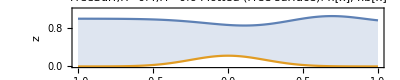

```mathematica
(* create plot *)
plotH=Plot[{(h[x] /.freeSurf)+hb[x],hb[x]},{x,-1,1},Filling->{1->{2}},PlotRange->{0,1.2},PlotLabel->(tag /.freeSurf)<>" Plotted (Free surface): h[x], hb[x]",ImageSize->{Automatic,plotHeight+labelHeight},FrameLabel->{"x","z"},Frame->True]
```